```mathematica
(**question no 1**)
```

```mathematica
?Hue
```

```mathematica
?Accumulate
```

```mathematica
?FindInstance
```

```mathematica
?List
```

```mathematica
(**Question No 02**)
```

```mathematica
n=40;
m=55;
```

```mathematica
a=Input[n]
```

```mathematica
40
```

```mathematica
b=Input[m]
```

55

```mathematica
Clear[n,m]
```

```mathematica
(**Question No 03**)
```

```mathematica
N[Sin[π/2],10]
```

1.

```mathematica
N[ArcTan[π/3],10]
```

0.8084487926

```mathematica
N[Log[ⅇ,125],10]
```

4.828313737

```mathematica
N[Log[10,125],10]
```

2.096910013

```mathematica
N[Log[2,125],10]
```

6.965784285

```mathematica
N[ⅇ^1,10]
```

2.718281828

```mathematica
(**question no 04**)
```

```mathematica
mylist={x,y,z,w};
```

```mathematica
Length[mylist]
```

4

```mathematica
Part[mylist,{3,4}]
```

{z,w}

```mathematica
Part[mylist,{1,3}]
```

{x,z}

```mathematica
Part[mylist,{1,2,3}]
```

{x,y,z}

```mathematica
(**Question No 05**)
```

```mathematica
Solve[3-11 x+x^2==0,x]
```

{{x→1/2 (11-√109)},{x→1/2 (11+√109)}}

```mathematica
Solve[-x+Cos[x]==0,x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

```mathematica
FindInstance[-x+Cos[x]==0,x,1]
```

{{x→Root0.739Root[{Cos[#1]-#1&,0.739085133215160641655312087674}]0.7390851332151607}}

```mathematica
(**Question No 06**)
```

```mathematica
Do[Print["A quick brown fox jumped over the lazy dog"],10]
```

A quick brown fox jumped over the lazy dog

A quick brown fox jumped over the lazy dog

A quick brown fox jumped over the lazy dog

«7 more identical outputs»

```mathematica
(**question No 07**)
```

```mathematica
?Fibonacci
```

```mathematica
Table[Fibonacci[n],{n,20}]
```

{1,1,2,3,5,8,13,21,34,55,89,144,233,377,610,987,1597,2584,4181,6765}

```mathematica
(**question No 08**)
```

```mathematica
?Floor
```

```mathematica
?Ceiling
```

```mathematica
Floor[Log10[100000]]
```

5

```mathematica
Ceiling[Log10[100000]]
```

5

```mathematica
(**Question No 09**)
```

```mathematica
f[x_]:=x^2+2x+3;
g[x_]:=√x;
f[g[x]]
```

3+2 √x+x

```mathematica
g[f[x]]
```

√(3+2 x+x^2)

```mathematica
(**Question No 10**)
```

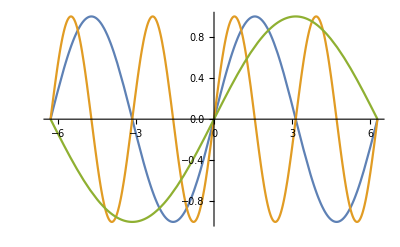

```mathematica
Plot[{Sin[x],Sin[2x],Sin[0.5x]},{x,-2π,2π}]
```

```mathematica
(**Question no 11**)
```

```mathematica
s={115,214,147,136,84,20,36,127,163,194,77,49,207,161,11,126,82,48,72,113,212,48,224,185,141,204,121,143,51,145};
```

```mathematica
Sort[{115,214,147,136,84,20,36,127,163,194,77,49,207,161,11,126,82,48,72,113,212,48,224,185,141,204,121,143,51,145}]
```

{11,20,36,48,48,49,51,72,77,82,84,113,115,121,126,127,136,141,143,145,147,161,163,185,194,204,207,212,214,224}

```mathematica
r=Sort[s];
```

```mathematica
Reverse[r]
```

{224,214,212,207,204,194,185,163,161,147,145,143,141,136,127,126,121,115,113,84,82,77,72,51,49,48,48,36,20,11}

```mathematica
Total[s]
```

3656